Check the hand calculations for problem 3.

```mathematica
AF[z_] = (1+z)^4/(16z^2) // Expand
af[u_] = AF[z]/. z-> E^(I u) // FullSimplify
af[u] // TrigReduce
```

3/8+1/(16 z^2)+1/(4 z)+z/4+z^2/16

Cos[u/2]^4

1/8 (3+4 Cos[u]+Cos[2 u])

Check the hand calculations for problem 2.

```mathematica
AF[u_] = (1/4)(1 + z + z^2 + z^3) /. z -> E^(I u)
AF2[u_] = (1/4) E^(3 I u /2) Sin[2 u] / Sin[u/2] // TrigToExp // Simplify
AF3[u_] = (1/2) (Cos[u/2] + Cos[3 u/2]) E^( 3 I u/2)// TrigToExp // Simplify
```

1/4 (1+ⅇ^(ⅈ u)+ⅇ^(2 ⅈ u)+ⅇ^(3 ⅈ u))

1/4 (1+ⅇ^(ⅈ u)+ⅇ^(2 ⅈ u)+ⅇ^(3 ⅈ u))

1/4 (1+ⅇ^(ⅈ u)+ⅇ^(2 ⅈ u)+ⅇ^(3 ⅈ u))

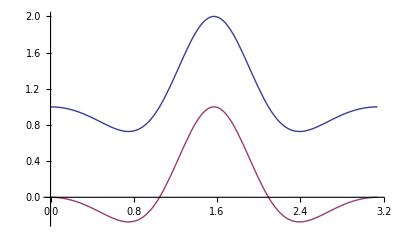

```mathematica
Plot[{1 + (1/4) Sin[ 2Pi Cos[t]]/Sin[Pi Cos[t]/2]  , (1/2)(Cos[Pi Cos[t]/2] + Cos[3Pi Cos[t]/2]) } ,{t, 0, Pi}]
```

```mathematica
(1/4) Sin[ 2Pi Cos[t]]/Sin[Pi Cos[t]/2]  -(1/2)(Cos[Pi Cos[t]/2] + Cos[3Pi Cos[t]/2]) // Simplify
```

0